```mathematica
SetDirectory["/home/lindorfer/ReWiTech/Masterarbeit/Programs/Simplified_A/Data/"]
```

/home/lindorfer/ReWiTech/Masterarbeit/Daten

```mathematica
<<ModList.m
```

```mathematica
docks ={{0,4140,0},{4140,5160,9},{0,2640,1},{2640,4620,8},{0,2460,2},{2460,4440,7},{0,2400,3},{2400,4500,6},{0,2280,4},{2280,4500,5}}
```

{{0,4140,0},{4140,5160,9},{0,2640,1},{2640,4620,8},{0,2460,2},{2460,4440,7},{0,2400,3},{2400,4500,6},{0,2280,4},{2280,4500,5}}

```mathematica
?Take2
```

Take2[list_, a_, b_] Takes the Elements a & b of a sublist in list. Example: Take2[{{a,b,c,d,},{a,b,c,d}}, 1, 2] = {{a,b},{a,b}}.

```mathematica
times=Take2[docks,1,2]
```

{{0,4140},{4140,5160},{0,2640},{2640,4620},{0,2460},{2460,4440},{0,2400},{2400,4500},{0,2280},{2280,4500}}

```mathematica
Take[times,{2,3}]
```

{{4140,5160},{0,2640}}

```mathematica
Flatten[{Take[times,{1,2}],Take[times,{3,4}],Take[times,{5,6}]},0]
```

{{{0,4140},{4140,5160}},{{0,2640},{2640,4620}},{{0,2460},{2460,4440}}}

```mathematica
differences=Map[#[[2]]-#[[1]]&,times]
```

{4140,1020,2640,1980,2460,1980,2400,2100,2280,2220}

```mathematica
Take[differences,{1,2}]
```

{4140,1020}

```mathematica
Take[differences,All,{2}]
```

Take::take: Cannot take positions 2 through 2 in 4140.

Take[{4140,1020,2640,1980,2460,1980,2400,2100,2280,2220},All,{2}]

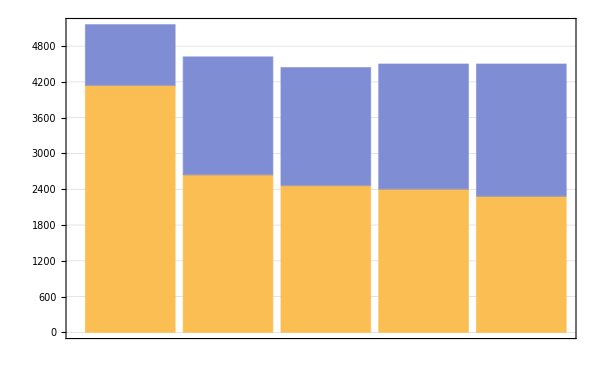

```mathematica
BarChart[{Take[differences,{1,2}],Take[differences,{3,4}],Take[differences,{5,6}],Take[differences,{7,8}],Take[differences,{9,10}]},
ChartLayout->"Stacked",
ImageSize->600,
Frame->True,
PlotTheme->"Detailed"]
```

```mathematica
d1={{0,1860,0},{1860,3720,5},{10000,11860,4},{15366,16806,9},{17822,19022,7},{21258,22278,0},{22568,23348,2},{26862,27642,3}};

d2={{0,1860,1},{1860,3720,6},{16680,17940,1},{18422,19502,3},{21590,22490,5},{27484,29224,8}};

d3={{0,1860,2},{1860,3720,7}};

d4={{0,1860,3},{1860,3720,8}};

d5={{0,1860,4},{1860,2880,9}};
```

```mathematica
d1=Take2[d1,1,2]
d2=Take2[d2,1,2]
d3=Take2[d3,1,2]
d4=Take2[d4,1,2]
d5=Take2[d5,1,2]
```

{{0,1860},{1860,3720},{10000,11860},{15366,16806},{17822,19022},{21258,22278},{22568,23348},{26862,27642}}

{{0,1860},{1860,3720},{16680,17940},{18422,19502},{21590,22490},{27484,29224}}

{{0,1860},{1860,3720}}

{{0,1860},{1860,3720}}

{{0,1860},{1860,2880}}

```mathematica
diffd1=Map[#[[2]]-#[[1]]&,d1];
diffd2=Map[#[[2]]-#[[1]]&,d2];
diffd3=Map[#[[2]]-#[[1]]&,d3];
diffd4=Map[#[[2]]-#[[1]]&,d4];
diffd5=Map[#[[2]]-#[[1]]&,d5];
```

```mathematica
getwaits[list_]:=Module[{i,waits={}},

For[i = 1, i <Length[list],i++,
AppendTo[waits,list[[i+1,1]]-list[[i,2]]];
];
Return[waits]
]
```

```mathematica
getbars[list1_,list2_]:=Module[{i,bars={}},

For[i=1, i< Length[list1],i++,

AppendTo[bars,list1[[i]]];
AppendTo[bars,list2[[i]]];
]
AppendTo[bars,list1[[Length[list1]]]];

Return[bars]
]
```

```mathematica
waitsd1=getwaits[d1]
waitsd2=getwaits[d2]
waitsd3=getwaits[d3]
waitsd4=getwaits[d4]
waitsd5=getwaits[d5]
```

{0,6280,3506,1016,2236,290,3514}

{0,12960,482,2088,4994}

{0}

{0}

{0}

```mathematica
barsd1=getbars[diffd1,waitsd1]
barsd2=getbars[diffd2,waitsd2]
barsd3=getbars[diffd3,waitsd3]
barsd4=getbars[diffd4,waitsd4]
barsd5=getbars[diffd5,waitsd5]
```

{1860,0,1860,6280,1860,3506,1440,1016,1200,2236,1020,290,780,3514,780}

{1860,0,1860,12960,1260,482,1080,2088,900,4994,1740}

{1860,0,1860}

{1860,0,1860}

{1860,0,1020}

```mathematica
color={};
For[i = 1, i< 15,i++,
AppendTo[color,Red];
AppendTo[color,White];
]
```

```mathematica
color
```

{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1]}

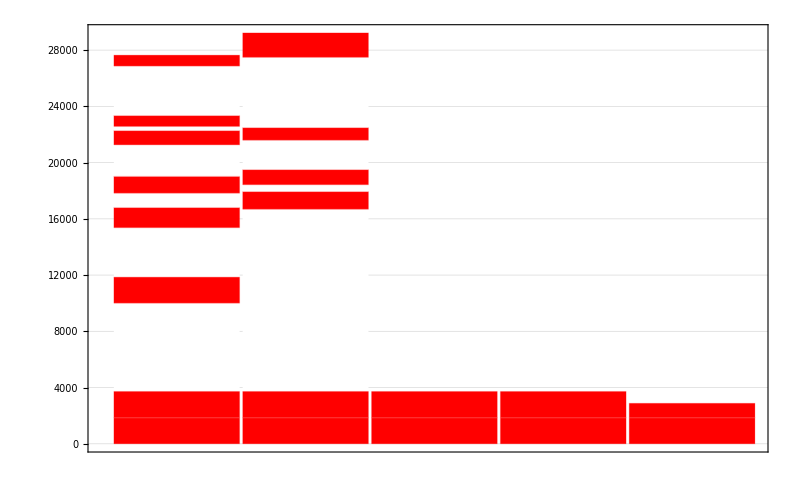

```mathematica
BarChart[{barsd1,barsd2,barsd3,barsd4,barsd5},
ChartLayout->"Stacked",
ImageSize->800,
Frame->True,
PlotTheme->"Detailed",
ChartStyle->color]
```

#### Initial Solution

```mathematica
t1={{18600,0,18600,4866,18600,7376,4200,2576,2400,486,16800},{18600,0,18600,6280,12300,268,6000,9762,2400},{18600,0,18600,12960,9600},{18600,0,18600,14702,8700},{18600,0,6000,30138,6900}};
```

#### 500 Steps opt_2 Solution

```mathematica
t2={{0,2400,18600,0,6000,0,18600,0,18600,8538,2400},{16800,1800,18600,138,2400,1662,6900,8838,12300},{8700,0,18600,12110,18600,2292,6000},{4200,0,18600,13448,18600,56,18600},{9600,2700,18600,2700,18600,6660,2400}};
```

#### 500 Steps swap_2_difftrucks Solution

```mathematica
t3={{2400,0,18600,0,18600,9842,18600,-10984,6900,5708,2400},{18600,6360,18600,2320,6000,2858,16800},{18600,0,12300,6300,18600,2102,9600},{6000,0,18600},{18600,2210,8700,0,18600,14050,4200}};
```

```mathematica
PlotBarChart[list_,max_]:=BarChart[list,
ChartLayout->"Stacked",
ImageSize->500,
Frame->True,
PlotTheme->"Detailed",
ChartStyle->color,
PlotRange->{All,{0,max}},
Epilog->{Black,Line[{{0.32,max},{100,max}}]}
]
```

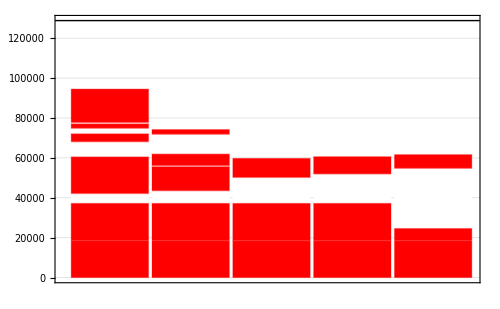

```mathematica
PlotBarChart[t1,128842]
```

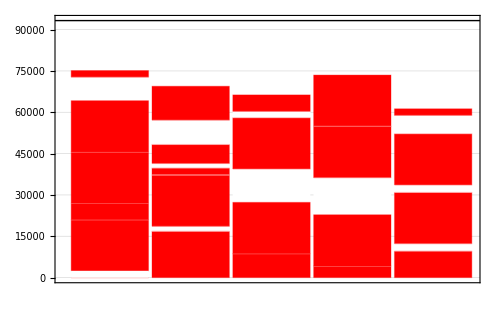

```mathematica
PlotBarChart[t2,93272]
```

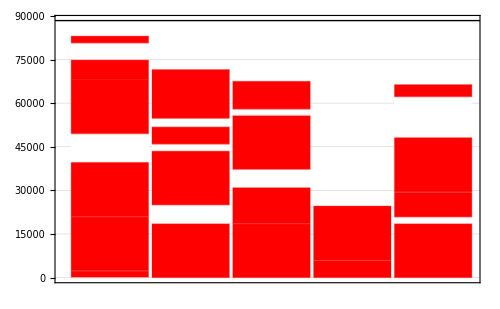

```mathematica
PlotBarChart[t3,88396]
```

#### Initial Solution

```mathematica
t1={{18600,0,18600,4866,18600,7376,4200,2576,2400,486,16800},{18600,0,18600,6280,12300,268,6000,9762,2400},{18600,0,18600,12960,9600},{18600,0,18600,14702,8700},{18600,0,6000,30138,6900}};
```

#### 500 Steps opt_2 + 50 swap2 + 500 opt_2 Solution

```mathematica
t2={{2400,0,4200,0,2400,0,6000,7800,18600,4500,6000,2304,18600},{18600,4266,6900,7076,18600},{18600,6902,18600,4564,18600},{8700,0,18600,6660,18600,2400,9600},{12300,8510,16800,3856,18600}};
```

```mathematica
PlotBarChart[t1,128842]
```

-Graphics-

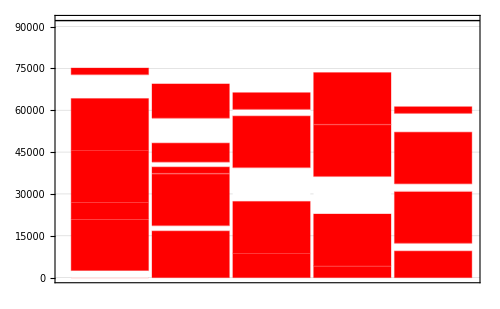

```mathematica
PlotBarChart[t2,92146]
```

```mathematica
t3={{2400,16200,18600,0,18600,0,18600},{6000,0,9600,666,6900,0,12300,0,18600,672,18600},{6000,0,16800,0,18600,242,18600,14460,4200},{18600,21000,8700,366,18600},{18600,44702,2400}};
PlotBarChart[t2,92146]
```

```mathematica
einf={{5000,2000,5000},{0,4000,1200,0}}
```

{{5000,2000,5000},{0,4000,1200,0}}

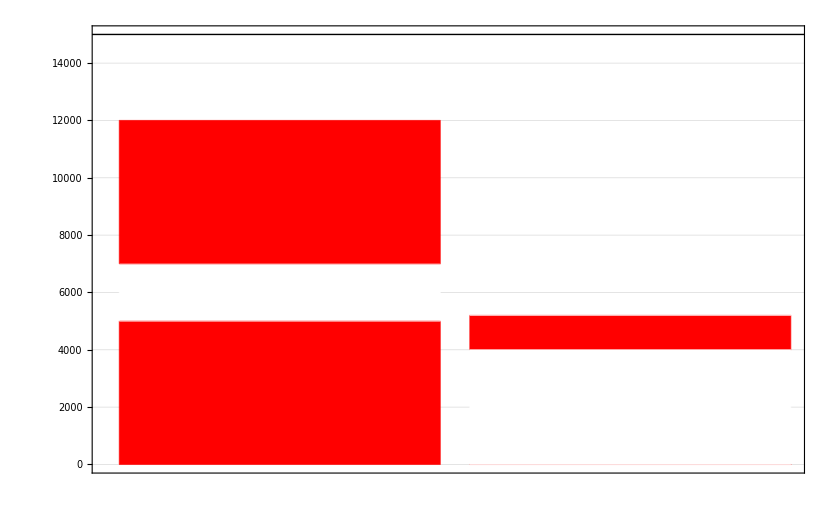

```mathematica
PlotBarChart[einf,15000]
```

```mathematica
vnssol={{2400,3600,18600,11648,18600,0,6000,8154,2400},{6900,0,18600,8404,18600},{18600,0,18600,8700,4200,5466,9600},{8700,0,18600,0,18600,0,12300},{6000,0,18600,6738,18600,0,16800}};
```

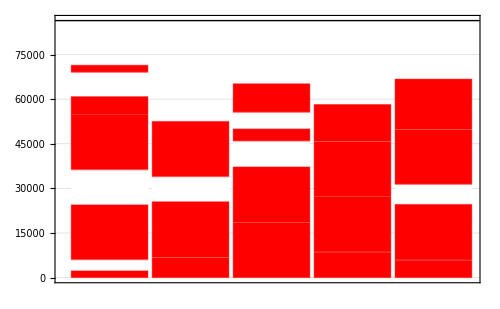

```mathematica
PlotBarChart[vnssol,86408]
```

```mathematica
vnssol2={{6000,0,2400,0,18600,0,18600,3066,16800},{18600,2210,12300,794,18600,7606,4200},{2400,0,18600,16200,18600},{6900,0,18600,5838,18600,8622,6000},{18600,3666,18600,5014,8700,3072,9600}};
```

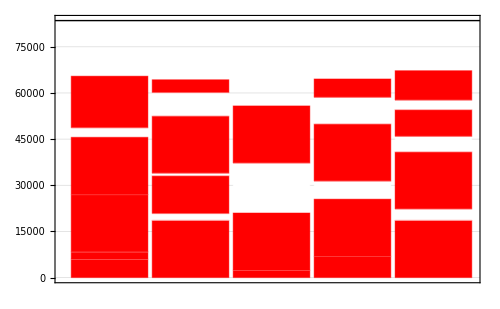

```mathematica
PlotBarChart[vnssol2,83520]
```

```mathematica
vnssol3={{6000,0,2400,0,18600,0,18600,3066,16800},{18600,2210,12300,794,18600,7606,4200},{2400,0,18600,16200,18600},{6900,0,18600,5838,18600,8622,6000},{18600,3666,18600,5014,8700,3072,9600}};
PlotBarChart[vnssol3,83520]
```

-Graphics-

```mathematica
vnssol4={{6000,0,2400,0,18600,0,18600,690,12300},{18600,2210,9600,6790,8700,0,18600},{2400,0,18600,12904,18600,6056,6000},{6900,0,18600,5838,18600,10172,4200},{18600,3666,18600,7800,16800}}
```

{{6000,0,2400,0,18600,0,18600,690,12300},{18600,2210,9600,6790,8700,0,18600},{2400,0,18600,12904,18600,6056,6000},{6900,0,18600,5838,18600,10172,4200},{18600,3666,18600,7800,16800}}

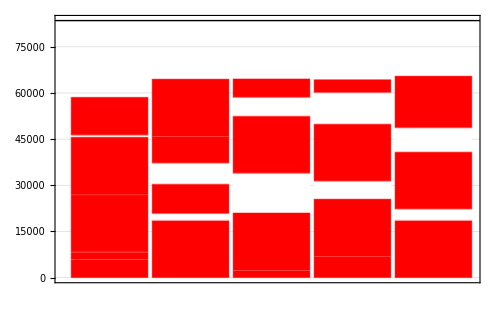

```mathematica
PlotBarChart[vnssol4,83520]
```

### Increase Docksize from 5 to 6

```mathematica
vnssol5={{6900,0,18600,13868,8700,13570,2400},{2400,0,18600,0,18600,3600,18600},{6000,0,18600,360,18600,2320,12300},{18600,12738,18600},{18600,30842,16800},{9600,6666,4200,5014,18600,4586,6000}};
```

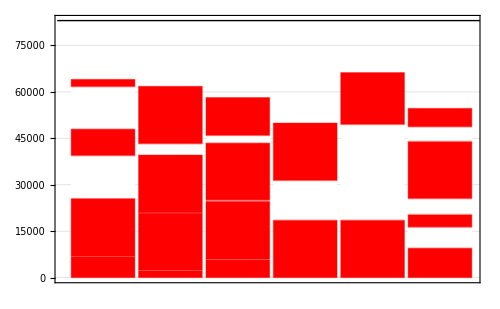

```mathematica
PlotBarChart[vnssol5,83042]
```

### Increase Docksize from 5 to 8

```mathematica
vnssol6={{18600,2210,4200},{2400,0,9600,4266,18600,1976,18600},{2400,3600,18600,19312,18600},{18600,18600,8700},{12300,15580,18600,2962,16800},{18600,30066,6000},{18600,36138,6000},{18600,31560,6900}};
```

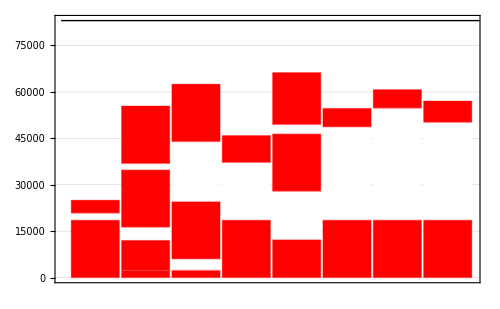

```mathematica
PlotBarChart[vnssol6,83042]
```

### Increase Docksize from 5 to 8

```mathematica
vnssol7={{18600,6360,18600},{6000,37480,6000},{18600,30066,6900},{18600,24880,8700},{18600,15000,18600,1010,2400,438,2400},{18600,18242,18600},{18600,31560,4200},{18600},{16800,35102,9600},{12300}};
```

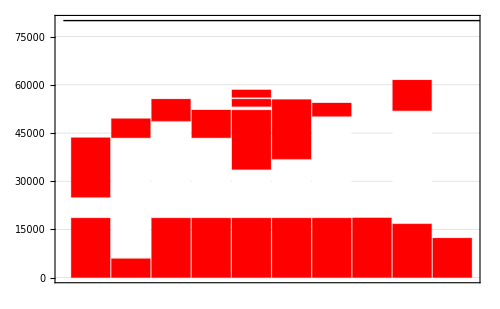

```mathematica
PlotBarChart[vnssol7,80004]
```

```mathematica
vnssol8={{18600,2210,18600,16638,2400},{9600,15880,18600},{2400,22560,18600},{4200,18902,18600},{18600,18600,18600},{6000,37480,16800},{18600,15304,12300},{18600,12738,18600},{6000,37480,8700},{6900}};
```

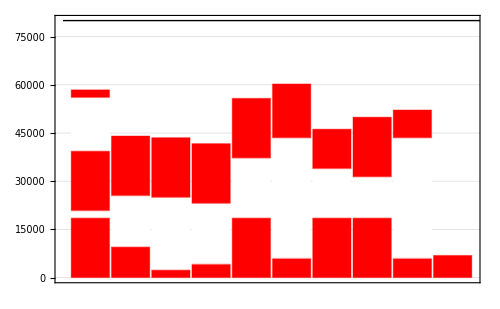

```mathematica
PlotBarChart[vnssol8,80004]
```

### Decrease Docksize from 5 to 2

```mathematica
initsol={{18600,0,18600,0,18600,0,18600,0,18600,0,12300,0,8700,0,6000,0,2400,6280,16800},{18600,0,18600,0,18600,0,18600,0,6000,0,18600,0,9600,0,6900,0,4200,0,2400}};
```

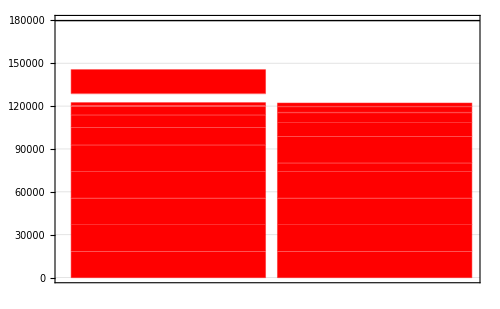

```mathematica
PlotBarChart[initsol,179818]
```

```mathematica
vnss2={{18600,0,18600,0,18600,0,18600,0,6000,0,18600,0,8700,0,6000,0,4200,0,2400,0,9600},{18600,0,6900,0,18600,0,18600,0,18600,0,18600,0,12300,0,16800,0,2400}};
```

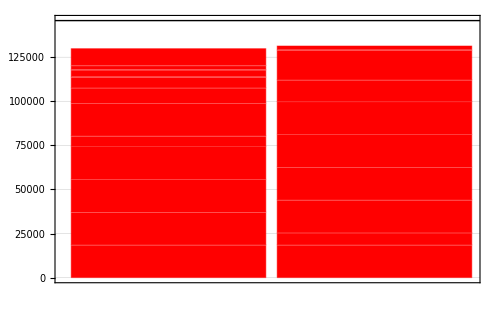

```mathematica
PlotBarChart[vnss2,145800]
```

### Decrease Docksize from 5 to 3

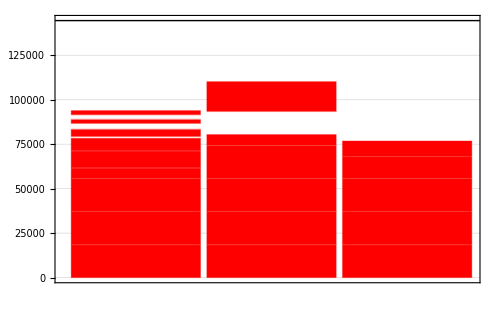

```mathematica
initsol3={{18600,0,18600,0,18600,0,6000,0,9600,0,6900,966,4200,3176,2400,2438,2400},{18600,0,18600,0,18600,0,18600,0,6000,12960,16800},{18600,0,18600,0,18600,0,12300,0,8700}};
PlotBarChart[initsol3,144498]
```

```mathematica
vnssol3={{6000,0,4200,0,18600,0,18600,0,18600,0,18600,0,2400},{18600,0,18600,0,18600,0,2400,0,12300,0,6900,0,9600},{18600,0,18600,0,6000,0,18600,0,8700,0,16800}};
```

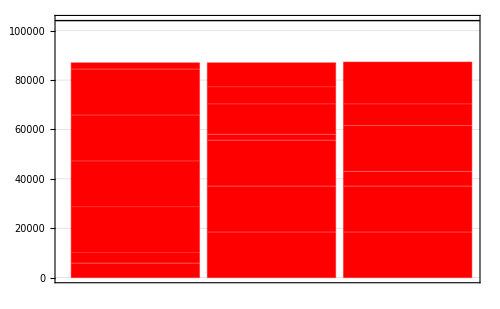

```mathematica
PlotBarChart[vnssol3,104100]
```

### Decrease Docksize from 5 to 4

```mathematica
initsol4={{18600,0,18600,0,18600,248,8700,3294,4200,8688,2400,952,16800},{18600,0,18600,0,6000,6960,18600,3050,2400},{18600,0,18600,14702,12300,0,6900},{18600,0,18600,17538,9600,0,6000}};
```

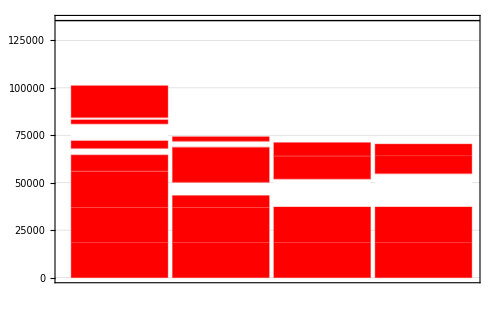

```mathematica
PlotBarChart[initsol4,135420]
```

```mathematica
vnssol4={{2400,0,18600,0,18600,0,18600,2402,9600},{8700,0,18600,6604,18600,0,16800},{6000,0,18600,0,6000,738,18600,0,12300},{6900,0,18600,0,18600,0,18600,0,4200,3542,2400}};
```

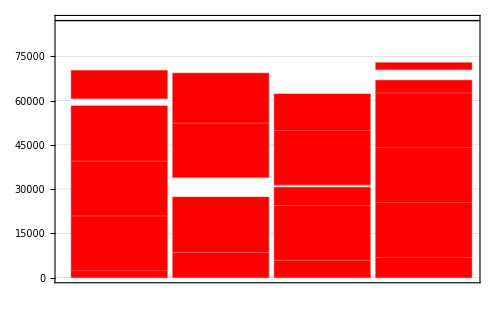

```mathematica
PlotBarChart[vnssol4,87114]
```